```mathematica
(*Box2g[u_]:=Rectangle[{Min[First[u]],Min[Last[u]]},{Max[First[u]],Max[Last[u]]}];
Box2g[ix_,iy_,u_]:=Module[{value,min,max,mid},
value={u[[ix]],u[[iy]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{Rectangle[min,max],PointSize[Large],Black,Point[mid]}
];

Pped2g[ix_,iy_, pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}
];

PpedD2g[ix_,iy_,pped2[x_,m_,u_, n_, v_]]:= Module[{x1,m1,u1,n1,v1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
n1={{n[[ix,ix]], n[[ix,iy]]},{n[[iy,ix]], n[[iy,iy]]}};
v1={v[[ix]], v[[iy]]};
(*GeometricTransformation[Rectangle[{Min[First[u1]]+Min[First[v1]],Min[Last[u1]]+Min[Last[v1]]},{Max[First[u1]]+Max[First[v1]],Max[Last[u1]]+Max[Last[v1]]}],AffineTransform[{m1,x1}]]];*)
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}];
*)

(**)

bThickness=0.01;
bPointSize=Small;
pPointSize=0.01;

pped2g[ix_,iy_,box[v_]]:=Module[{value,min,max,mid},
value={v[[ix]],v[[iy]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{EdgeForm[{Thickness[bThickness],bColor}],FaceForm[Opacity[0.1,LightGray]],Rectangle[min,max],PointSize[bPointSize](*,Black,Point[mid]*)}
];
pped2g[ix_,iy_,pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[pPointSize],Red,Point[x1]}
];

pped2intv[iy_,box[v_]]:={{LightGray,PointSize[bPointSize]},v[[iy]]};
pped2intv[iy_,pped[x_,m_,u_]]:=Module[{ix=1,x1,m1,u1,ps,ys},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
ps={{Min[u[[ix]]],Min[u[[iy]]]},{Min[ u[[ix]]],Max[ u[[iy]]]},{Max[ u[[ix]]],Min[ u[[iy]]]},{Max[ u[[ix]]],Max[ u[[iy]]]}};
ps=(m1.#)+x1&/@ps;
ys=#[[2]]&/@ps;
{{Red,PointSize[pPointSize]},Interval[{Min[ys],Max[ys]}]}
];

pipe2g[ix_,iy_,{t_,pped_}]:=Module[{res,value,min,max,mid},
If[ix>0,pped2g[ix,iy,pped],
res=pped2intv[iy,pped];
value={t,res[[2]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
Join[{EdgeForm[{Thickness[bThickness],bColor}],FaceForm[Opacity[0.1,LightGray]],Rectangle[min,max]},Append[res[[1]],Point[mid]]]
]
];
pipe2g[tmax_,ix_,iy_,{t_,pped_}]:=Module[{},
(*Print[tmax,t];*)
If[Min[t]<tmax,pipe2g[ix,iy,{t,pped}],{}]];
```

```mathematica
pped2g[ix1_,ix2_,ix3_,box[v_]]:=Module[{value,min,max,mid},
value={v[[ix1]],v[[ix2]],v[[ix3]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{(*EdgeForm[{Thin,Black}],FaceForm[Opacity[0.1,LightGray]],Cuboid[min,max],*)PointSize[bPointSize],Black,Point[mid]}
];
pped2g[ix1_,ix2_,ix3_,pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix1]],x[[ix2]], x[[ix3]]}; 
m1={{m[[ix1,ix1]], m[[ix1,ix2]], m[[ix1,ix3]]},{m[[ix2,ix1]], m[[ix2,ix2]], m[[ix2,ix3]]},{m[[ix3,ix1]],m[[ix3,ix2]],m[[ix3,ix3]]}};
u1={u[[ix1]],u[[ix2]],u[[ix3]]};
{(*EdgeForm[{bThickness,Black}],FaceForm[Opacity[0.1,LightGray]],*)(*GeometricTransformation[Cuboid[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],*)
PointSize[pPointSize],Red,Point[x1]}
];

pipe2g[ix1_,ix2_,ix3_,{t_,pped_}]:=Module[{res,value,min,max,mid},
If[ix1>0,pped2g[ix1,ix2,ix3,pped],
res=pped2intv[ix3,pped];
value={t,res[[2]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
Join[{EdgeForm[{bThickness,Black}],FaceForm[Opacity[0.1,LightGray]],Cuboid[min,max]},Append[res[[1]],Point[mid]]]
(*Print[value];
Print[min];
Print[max]*)
]
];
```

```mathematica
Export["gg.eps",gg]
```

gg.eps

```mathematica
Export["gg2.png",gg,ImageSize->1000]
```

gg2.png

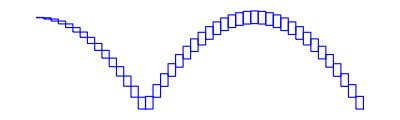

```mathematica
SetDirectory[NotebookDirectory[]];
list = <<"../src_ocaml/pped.dat";
list=list[[1;;-2]];
bThickness=0.002;
bPointSize=0.001;
pPointSize=0.001;
bColor=Blue;
length=100;
g1=Graphics[pipe2g[length,0,2,#]& /@ list];
g2=Graphics[pipe2g[length,0,2,#]& /@ list];
(*g2=Plot[{Sin[t+Pi/6],1,-15},{t,0,length},PlotStyle->{Thickness[0.003]}];*)
g3=Plot[1,{t,0,length},PlotStyle->{Red}];
gg=Show[{g1(*,g2,g3*)},Axes->Automatic,AxesStyle->Directive[12],AspectRatio->3/10]
```

```mathematica
SetDirectory[NotebookDirectory[]];
list = <<"../src_ocaml/pped.dat";
list=list[[1;;-2]];
bThickness=0.001;
bPointSize=0.001;
pPointSize=0.001;
bColor=Black;
length=20;
g1=Graphics3D[pipe2g[1,2,3,#]& /@ list]
(*gg=Show[{g1(*,g2,g3*)},Axes->Automatic,AxesStyle->Directive[10]]*)
```

-Graphics3D-